# Exploring Kyle’s Matrix

Looking at the main matrix.

```mathematica
SetDirectory["C:\\Users\\struther\\Desktop\\2022-23-Classes\\5631\\SampleMatrices\\Week2_Kyle"];
MessyData=ReadList["allTerms.txt",{Character,Number,Character,Number,Character,Real,Character}];
ZeroBaseData=MessyData⟦All,{2,4,6}⟧;
nz=Length[ZeroBaseData];
A=SparseArray[Table[
{i,j,a}=ZeroBaseData⟦k⟧+{1,1,0.0};
{i,j}->a,
{k, nz}]];
TabView[{
"A"->MatrixPlot[A,PlotLegends->Automatic],
span=Span[m1,m2];
"CloseUp"->MatrixPlot[A⟦span,span⟧,PlotLegends->Automatic,PlotLabel->StringForm["``:``",m1,m2],
DataRange->{{m1,m2},{m1,m2}}]
}]
```

12

## Spectrum

As we will soon understand matrix eigenvalues determine the convergence of iterative schemes. Preconditioning tries to create equivalent linear algebra problems with better convergence properties. The matrix is is just small enough to compute all the eigenvalues!  I am going to look at the biggest eigenvalues and eigenvectors first

```mathematica
{λs,Vs}=Eigensystem[A,256];
TabView[{
"Vs"->MatrixPlot[Abs[Vs],
PlotLegends->Automatic],
"λs"->ListPlot[ReIm[λs],PlotRange->All]
},2]
```

12

There are some big “almost-real” eigenvalues! The matching evecs have some common structure.

It takes longer to look at the smallest eigenvalues! The structure is funky here! The smallest eigenvalues have roughly 	
	||λ||≈1.

```mathematica
{λs,Vs}=Eigensystem[A,-256];
TabView[{
"Vs"->MatrixPlot[Abs[Vs],
PlotLegends->Automatic],
"λs"->ListPlot[ReIm[λs],PlotRange->All]
},2]
```

12

Does everyone (or maybe anyone) understand why it might take longer to compute small eigenvalues?

The condition number of the matrix is about 3×10^6.

Does everyone (or maybe anyone) understand why this is fine for a direct solver?

## Preconditioning

The basic idea is that we want an equivalent problem to 
	A.x=b
which has a “better conditioned” matrix. For our first pass, note the biggest bits of A are near the diagonal and remember banded matrices are easy to do things with.

12

I am going to eyeball that the middle “stripe” is about 160 wide. It is not obvious but that middle stripe is also symmetric.

```mathematica
band=160;
{m1,m2}={3500,4500};
ADia=LowerTriangularize[UpperTriangularize[A,-band],band];
TabView[{
"ADia"->MatrixPlot[ADia,PlotLegends->Automatic],
"A-ADia"->MatrixPlot[A-ADia,PlotLegends->Automatic],
span=Span[m1,m2];
"CloseUp ADia"->MatrixPlot[ADia⟦span,span⟧,PlotLegends->Automatic,PlotLabel->StringForm["``:``",m1,m2],
DataRange->{{m1,m2},{m1,m2}}],
"CloseUp A-ADia"->MatrixPlot[(A-ADia)⟦span,span⟧,PlotLegends->Automatic,PlotLabel->StringForm["``:``",m1,m2],
DataRange->{{m1,m2},{m1,m2}}],
"ADia-ADiaᵀ"->MatrixPlot[ADia-ADiaᵀ,PlotLegends->Automatic,PlotLabel->Norm[Flatten[ADia-ADiaᵀ],∞]]
}]
```

12345

The good thing about the diagonal chunk of A is that you can easily solve linear systems and compute eigenvalues of A_dia.  The bad news is it is not A.  In some meaningful sense it is about 85% of A.

```mathematica
Norm[A-ADia,"Frobenius"]/Norm[A,"Frobenius"]
```

0.16936

The preconditioning idea is to think that if we have a simple, invertible approximation M to A (or equivalently an approximation to A^-1) then we can write down a better matrix Â that solves the same problem since
	A.x=b ⟹ M^-1.A.x=M^-1.b ⟹ Â.x=b̂
The other side also works
	A.x=b ⟹ A.M^-1.M.x=b ⟹ Ã.y=b and y=M.x
You can also do both sides!  The question is how good a preconditioner does our diagonal trick give?

Just as a demo that you can do all sorts of things with our banded preconditioner.  Here are the eigenvalues.  It has condition number about 10^6.

{4.84915×10^6,0.768498}

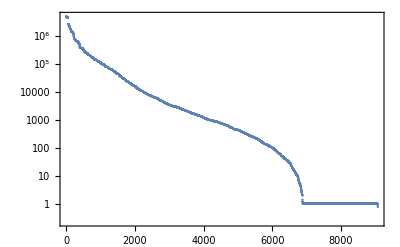

```mathematica
λDia = Eigenvalues[ADia,Method->"Banded"];
{Max[λDia],Min[λDia]}
ListLogPlot[λDia,Frame->True,FrameTicks->Automatic]
```

Direct methods work well on this banded matrix! You can perform an LU decomposition is fast!  You can compute the largest eigenvalue easily using the power method.

```mathematica
x=RandomReal[{-1,1},Length[A]];
LinSolFun=LinearSolve[ADia,Method->"Banded"];

Do[MInvAx=A.LinSolFun[x];x=Normalize[MInvAx],300];λ=Norm[MInvAx];
ListPlot[{x,A.LinSolFun[x]}ᵀ,
PlotRange->All,
Prolog->{Directive[LightPink,Thickness[0.02]],Line[{{-1,-λ},{1,λ}}]}]
```

-Graphics-